```mathematica
ClearAll["Global`*"];
```

# Lists (Arrays)

## List Generation

```mathematica
l1={1,2,3,4,5}
l2=Range[10]
l3=Range[7,22,3]
```

{1,2,3,4,5}

{1,2,3,4,5,6,7,8,9,10}

{7,10,13,16,19,22}

## List Operations

### Slice (Part)/Take

```mathematica
list = {a, b, c, d, e};
Take[list, 2]
Take[list,-2]
Take[list, {2,4}]
list[[2]]
list[[2;;4]]
Part[list,3]
```

{a,b}

{d,e}

{b,c,d}

b

{b,c,d}

c

### Updating a List

```mathematica
list= {a, b, c, d, e}
list[[3]]=f;
list
```

{a,b,c,d,e}

{a,b,f,d,e}

```mathematica
l1=Range[10]
l2=Range[4,22,3]
Join[l1,l2]
Union[l1,l2]
Intersection[l1,l2]
```

{1,2,3,4,5,6,7,8,9,10}

{4,7,10,13,16,19,22}

{1,2,3,4,5,6,7,8,9,10,4,7,10,13,16,19,22}

{1,2,3,4,5,6,7,8,9,10,13,16,19,22}

{4,7,10}

### Map on List

```mathematica
f[x_]:=x^2+1;
list={-5, -2, 0, 1, 3};
Map[f, list]
f/@list
```

{26,5,1,2,10}

{26,5,1,2,10}

### Duplicates

```mathematica
list={"a", "b", "b", "c", "c", "c", "d"};
FindDuplicates[list_]:=Module[
{test},
test=DuplicateFreeQ[list];
If[test,
{},
Part[Select[Tally@list,Part[#, 2]>1&],All,1]
]
];
FindDuplicates[list]
```

{b,c}

## Matrices & Tables

### Generation

```mathematica
IdentityMatrix[3]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
DiagonalMatrix[Table[RandomInteger[100],5]]//MatrixForm
```

(33 | 0 | 0 | 0 | 0
0 | 42 | 0 | 0 | 0
0 | 0 | 36 | 0 | 0
0 | 0 | 0 | 55 | 0
0 | 0 | 0 | 0 | 82)

```mathematica
ConstantArray[2,10]
```

{2,2,2,2,2,2,2,2,2,2}

1 | 2 | 3
4 | 5 | 6
7 | 8 | 9

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

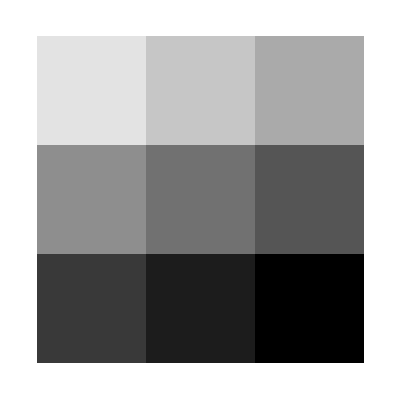

```mathematica
m={
{1,2,3},
{4,5,6},
{7,8,9}
};
TableForm[m]
MatrixForm[m]
ArrayPlot[m]
```

```mathematica
t1=Table[i,{i,1,10}];
t1//TableForm
t2=Table[{i,j},{i,1,5},{j,1,3}];
t2//MatrixForm
t3=Table[RandomInteger[10],{i,1,5},{j,1,5}];
t3//MatrixForm
```

1
2
3
4
5
6
7
8
9
10

((1
1) | (1
2) | (1
3)
(2
1) | (2
2) | (2
3)
(3
1) | (3
2) | (3
3)
(4
1) | (4
2) | (4
3)
(5
1) | (5
2) | (5
3))

(5 | 8 | 6 | 10 | 5
9 | 0 | 6 | 5 | 0
2 | 0 | 9 | 8 | 10
5 | 1 | 6 | 10 | 4
1 | 10 | 7 | 9 | 10)

### Manipulation

#### Matrix Operations

```mathematica
Table[RandomInteger[10],{i,1,5},{j,1,5}];
%//MatrixForm
Inverse[%%]//MatrixForm
Flatten[%]
```

(9 | 5 | 2 | 3 | 2
10 | 7 | 2 | 3 | 6
7 | 7 | 9 | 6 | 10
2 | 2 | 7 | 5 | 3
3 | 9 | 9 | 10 | 7)

(-7/80 | 73/280 | -43/280 | 151/560 | -53/560
31/32 | -137/112 | 83/112 | -255/224 | 45/224
27/32 | -125/112 | 79/112 | -155/224 | 1/224
-177/160 | 823/560 | -573/560 | 1361/1120 | -3/1120
-57/80 | 223/280 | -93/280 | 281/560 | -43/560)

{-7/80,73/280,-43/280,151/560,-53/560,31/32,-137/112,83/112,-255/224,45/224,27/32,-125/112,79/112,-155/224,1/224,-177/160,823/560,-573/560,1361/1120,-3/1120,-57/80,223/280,-93/280,281/560,-43/560}